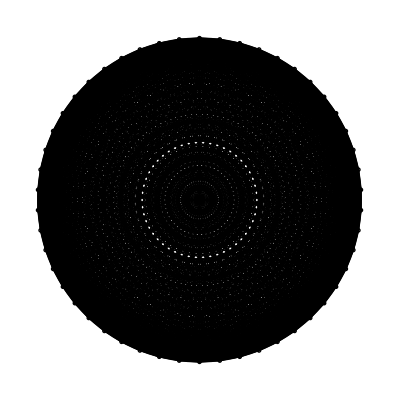

```mathematica
DreamCatcher[n_]:=Module[
{Δθ,Centers, Circles, Web,Diagonals},
Δθ=2π/(n);
Centers = Table[{n Cos[i*Δθ+π/2],n Sin[i*Δθ+π/2]},{i,n}];
Circles=Table[Circle[Centers⟦i⟧,0.5],{i,n}];
Web = Table[Line[{Centers⟦i⟧,Centers⟦j⟧}],{j,n},{i,j}];
Diagonals = If[OddQ[n],Table[Line[{{0,0},Centers⟦i⟧}],{i,n}],{}];
Graphics[{Web,Circles,Diagonals,Circle[{0,0},n]}]
]
DreamCatcher[50]
```